# Fancy Maps

## Color Palette

```mathematica
originalColorsValues={
{70,50,0,0},
{0,100,0,0},
{0,0,0,0},
{100,100,100,100},
{0,0,0,0}
};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues
```

{CMYKColor[Rational[7, 10], Rational[1, 2], 0, 0],CMYKColor[0, 1, 0, 0],CMYKColor[0, 0, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

## Generate Map

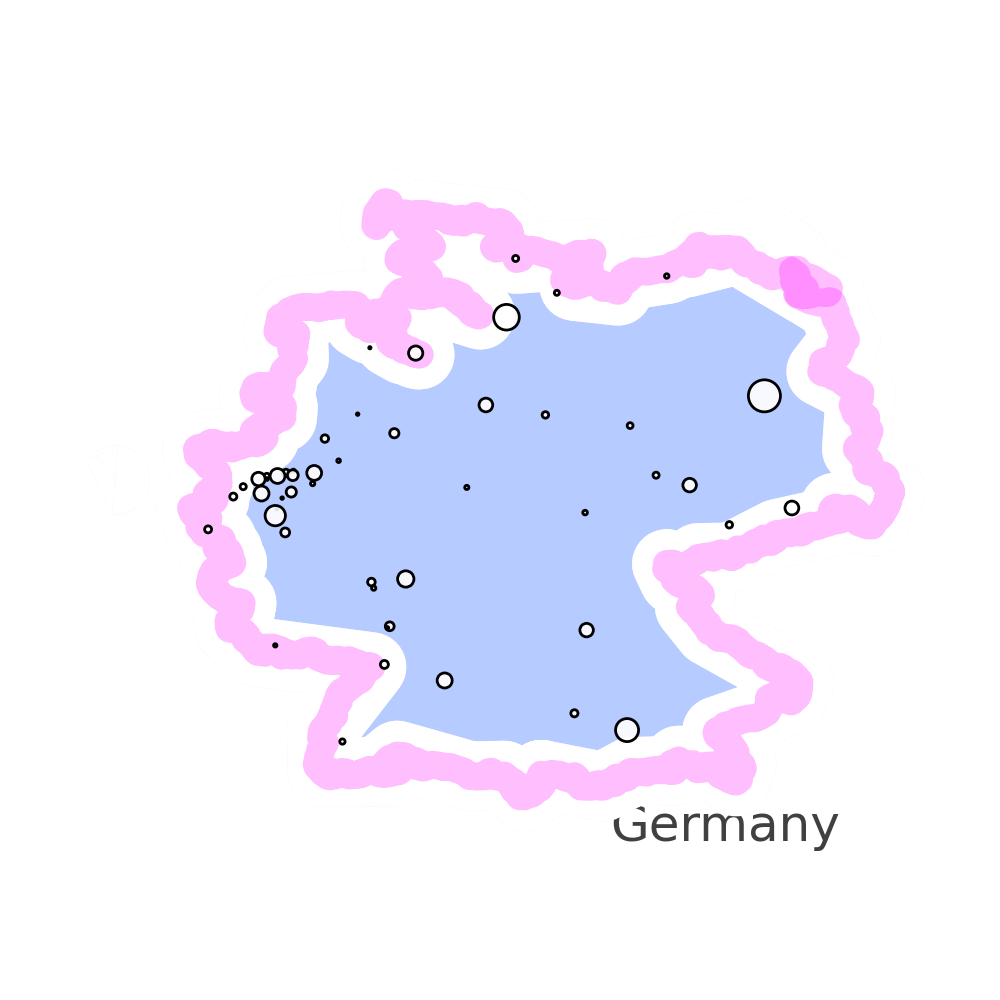

./fancyMapGermany.png

```mathematica
countryName="Germany";
popsNumber=50;
SetDirectory[NotebookDirectory[]];
(**)
populations=Normal[CityData[#,"Population"]&/@CityData[{All,countryName}]];
selectedPopSizes=(Reverse[populations//Sort])[[1;;popsNumber]];
indices=Flatten[Position[populations,#]&/@selectedPopSizes];
(**)
latLongs=Reverse[CityData[#,"Coordinates"]]&/@CityData[{All,countryName}][[indices]];
populations=populations[[indices]];
missingNo=Position[latLongs,Missing["NotAvailable"]]//Flatten;
latLongs=Delete[latLongs,missingNo];
populations=Delete[populations,missingNo];
(**)
ordering=(Reverse/@latLongs)//Ordering//Reverse;
{latLongs,populations}={latLongs[[ordering]],populations[[ordering]]};
(**)
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
minMaxes={Min[#],Max[#]}&/@(latLongs//Transpose);
center=Mean/@minMaxes;
gridSize=Max[Abs[(#[[1]]-#[[2]])]&/@minMaxes]*.7;
(**)
GeoGraphics[{
(*Quiet[GeoPosition/@CityData[{All,countryName}]],*)
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[.5],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->1
,Axes->False
(*,Background->Directive[{colorPalette[[5]],Opacity[1]}]*)
(*,Frame->True*)
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
(*,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]*)
,ImageSize->1000
,PlotRange->({#-gridSize,#+gridSize}&/@center)
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.002],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],0.01+#[[2]]/10]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[1],
Text[
Style[countryName,50,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.55gridSize,center[[2]]-gridSize*.8}]
}
]
Export["./fancyMap"<>countryName<>".png",%,ImageSize->2500,ImageResolution->500]
```